```mathematica
a = 2;
k = 1.0;
Clear[x, y,a,b, k, aa,bb,cc]
b = a;
a = 2;
u =Exp[-100*(x^2+y^2)]*Cos[Pi*x]*Cos[Pi*y]
```

ⅇ^(-100 (x^2+y^2)) Cos[π x] Cos[π y]

```mathematica
dux =  D[u, x]
duy = D[u, y]
FullSimplify[dux]
FullSimplify[duy]
```

-200 ⅇ^(-100 (x^2+y^2)) x Cos[π x] Cos[π y]-ⅇ^(-100 (x^2+y^2)) π Cos[π y] Sin[π x]

-200 ⅇ^(-100 (x^2+y^2)) y Cos[π x] Cos[π y]-ⅇ^(-100 (x^2+y^2)) π Cos[π x] Sin[π y]

-ⅇ^(-100 (x^2+y^2)) Cos[π y] (200 x Cos[π x]+π Sin[π x])

-ⅇ^(-100 (x^2+y^2)) Cos[π x] (200 y Cos[π y]+π Sin[π y])

```mathematica
qx = - dux * k
qy = - duy * k
FullSimplify[qx]
FullSimplify[qy]
```

k (200 ⅇ^(-100 (x^2+y^2)) x Cos[π x] Cos[π y]+ⅇ^(-100 (x^2+y^2)) π Cos[π y] Sin[π x])

k (200 ⅇ^(-100 (x^2+y^2)) y Cos[π x] Cos[π y]+ⅇ^(-100 (x^2+y^2)) π Cos[π x] Sin[π y])

ⅇ^(-100 (x^2+y^2)) k Cos[π y] (200 x Cos[π x]+π Sin[π x])

ⅇ^(-100 (x^2+y^2)) k Cos[π x] (200 y Cos[π y]+π Sin[π y])

```mathematica
f = D[qx, x] + D[qy, y]
FullSimplify[f]
```

k (200 ⅇ^(-100 (x^2+y^2)) Cos[π x] Cos[π y]+ⅇ^(-100 (x^2+y^2)) π^2 Cos[π x] Cos[π y]-40000 ⅇ^(-100 (x^2+y^2)) x^2 Cos[π x] Cos[π y]-400 ⅇ^(-100 (x^2+y^2)) π x Cos[π y] Sin[π x])+k (200 ⅇ^(-100 (x^2+y^2)) Cos[π x] Cos[π y]+ⅇ^(-100 (x^2+y^2)) π^2 Cos[π x] Cos[π y]-40000 ⅇ^(-100 (x^2+y^2)) y^2 Cos[π x] Cos[π y]-400 ⅇ^(-100 (x^2+y^2)) π y Cos[π x] Sin[π y])

2 ⅇ^(-100 (x^2+y^2)) k (-200 π x Cos[π y] Sin[π x]+Cos[π x] ((π^2-200 (-1+100 x^2+100 y^2)) Cos[π y]-200 π y Sin[π y]))

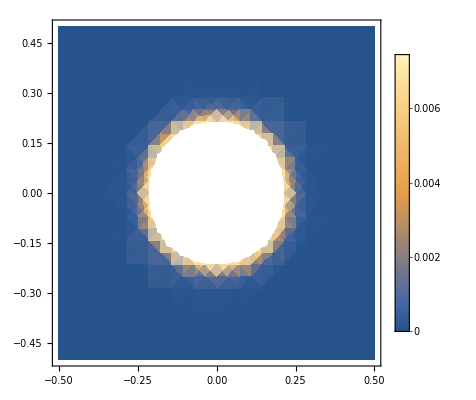

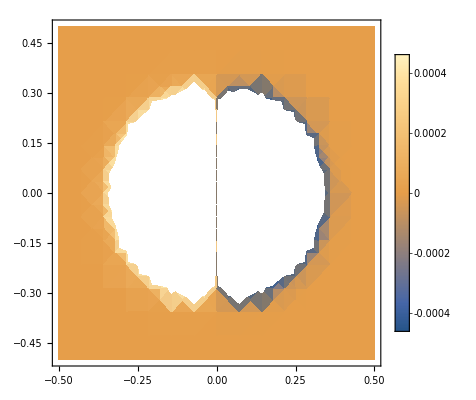

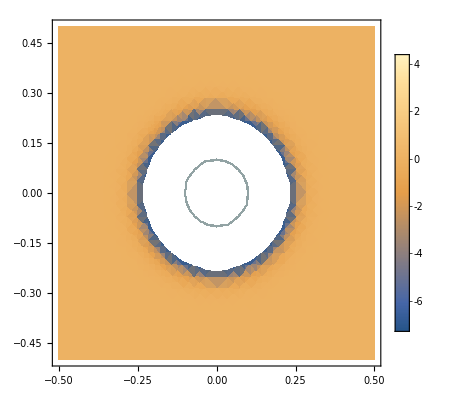

```mathematica
DensityPlot[u,{x,-0.5,0.5},{y,-0.5,0.5},PlotTheme->"Detailed"]
DensityPlot[dux,{x,-0.5,0.5},{y,-0.5,0.5},PlotTheme->"Detailed"]
DensityPlot[f,{x,-0.5,0.5},{y,-0.5,0.5},PlotTheme->"Detailed"]
```

```mathematica
k=1
x=0.5
qx
```

1

0.5

3.14159 ⅇ^(-100 (0.25+y^2)) Cos[π y]

```mathematica
FullSimplify[qx]
```

4.36303×10^-11 ⅇ^(-100 y^2) Cos[π y]

```mathematica
y= 0
```

0

```mathematica
qx
```

4.36303×10^-11

```mathematica
u
```

8.50391×10^-28